```mathematica
f1[x_] := -r0/(2Δr)+x/(3Δr)
FullSimplify[f1[r0+Δr](r0+Δr)^2-f1[r0] r0^2]
```

-Δr^2/24+(3 k^2 vx^2 ρ σx)/(4 p0^2 π (λ+2 μ))

```mathematica
FullSimplify[r0^3/(6 Δr)+(r0+Δr)^2 (-r0/(2 Δr)+(r0+Δr)/(3 Δr))]
```

1/6 Δr (3 r0+2 Δr)

```mathematica
1/T^2 2 ⅇ^(-((k0+k1) (ⅈ h Q+T))/Q) p0^2 Q (a^2 f1[a]-b^2 f1[b])^2 (-(ⅇ^(ⅈ h k0+(k0 T)/Q)-2 ⅇ^(ⅈ h (k0+k1)+(k0 T)/Q)+ⅇ^(ⅈ h (k0+2 k1)+(k0 T)/Q)-ⅇ^(ⅈ h k1+(k1 T)/Q)+2 ⅇ^(ⅈ h (k0+k1)+(k1 T)/Q)-ⅇ^(ⅈ h (2 k0+k1)+(k1 T)/Q)) T-ⅈ ⅇ^(((k0+k1) (ⅈ h Q+T))/Q) h Q (ExpIntegralEi[-ⅈ h k0-(k0 T)/Q]-ExpIntegralEi[ⅈ h k0-(k0 T)/Q]-ExpIntegralEi[-ⅈ h k1-(k1 T)/Q]+ExpIntegralEi[ⅈ h k1-(k1 T)/Q])+2 ⅇ^(ⅈ h (k0+k1)) h (ⅇ^((k1 T)/Q) (Q+k0 T) SinIntegral[h k0]-ⅇ^((k0 T)/Q) (Q+k1 T) SinIntegral[h k1]))
```

```mathematica
Energy[ρ_,σx_,vx_,Δr_,r0_,h_,Q_,T_,k0_,k1_,p0_,λ_,μ_,k_]:=1/T^2 2 ⅇ^(-((k0+k1) (ⅈ h Q+T))/Q) p0^2 Q (a^2 f1[a]-b^2 f1[b])^2 (-(ⅇ^(ⅈ h k0+(k0 T)/Q)-2 ⅇ^(ⅈ h (k0+k1)+(k0 T)/Q)+ⅇ^(ⅈ h (k0+2 k1)+(k0 T)/Q)-ⅇ^(ⅈ h k1+(k1 T)/Q)+2 ⅇ^(ⅈ h (k0+k1)+(k1 T)/Q)-ⅇ^(ⅈ h (2 k0+k1)+(k1 T)/Q)) T-ⅈ ⅇ^(((k0+k1) (ⅈ h Q+T))/Q) h Q (ExpIntegralEi[-ⅈ h k0-(k0 T)/Q]-ExpIntegralEi[ⅈ h k0-(k0 T)/Q]-ExpIntegralEi[-ⅈ h k1-(k1 T)/Q]+ExpIntegralEi[ⅈ h k1-(k1 T)/Q])+2 ⅇ^(ⅈ h (k0+k1)) h (ⅇ^((k1 T)/Q) (Q+k0 T) SinIntegral[h k0]-ⅇ^((k0 T)/Q) (Q+k1 T) SinIntegral[h k1]))
```

```mathematica
f0 = 0.004;
f1 = 2;
v = 1000;
```

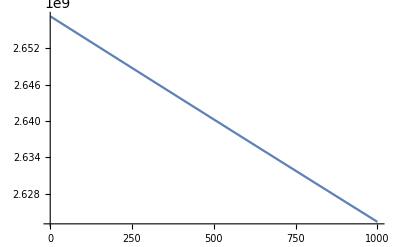

```mathematica
Q = 650;
ρ = 3.3 * 10^6;
σx = 10^-7*10^-4;
vx = 250000;
k0 =2π f0/v;
k1 = 2π f1/v;
p0 = 10^8;
λ = 7.2*10^10;
μ = 7.2*10^10;
k = 1.2*10^11;
h = 1.7*10^6;
Δr = 1;
Plot[{Re[Energy[ρ,σx,vx,Δr,r0,h,Q,T,k0,k1,p0,λ,μ,k]]},{T,1,10^3}]
```

```mathematica
r0 = k^2/(λ+2μ)3/(2π Δr)(ρ σx vx^2)/p0^2-3/4 Δr;
```

```mathematica
(λ+2μ)/k^2(1/6 Δr (3 r0+2 Δr))^2 2 p0^2
```

```mathematica
FullSimplify[(p0^2 Δr^2 (λ+2 μ) (2 Δr+3 (-(3 Δr)/4+(3 k^2 vx^2 ρ σx)/(2 p0^2 π Δr (λ+2 μ))))^2)/(18 k^2)]
```

((p0^2 π Δr^2 (λ+2 μ)-18 k^2 vx^2 ρ σx)^2)/(288 k^2 p0^2 π^2 (λ+2 μ))

```mathematica
Solve[(λ+2μ)/k^2 1/6 p0^2 π Δr h(4 r0 + 3Δr) == ρ σx vx^2 h,r0]
```

{{r0→-(3 (p0^2 π Δr^2 λ+2 p0^2 π Δr^2 μ-2 k^2 vx^2 ρ σx))/(4 p0^2 π Δr (λ+2 μ))}}

```mathematica
r0 = -(3 (p0^2 π Δr^2 λ+2 p0^2 π Δr^2 μ-2 k^2 vx^2 ρ σx))/(4 p0^2 π Δr (λ+2 μ))
```

-(3 (p0^2 π Δr^2 λ+2 p0^2 π Δr^2 μ-2 k^2 vx^2 ρ σx))/(4 p0^2 π Δr (λ+2 μ))

```mathematica
FullSimplify[(λ+2μ)/k^2(-Δr^2/24+(3 k^2 vx^2 ρ σx)/(4 p0^2 π (λ+2 μ)))^2 2 p0^2]
```

(2 (λ+2 μ) ((p0 Δr^2)/24-(3 k^2 vx^2 ρ σx)/(4 p0 π λ+8 p0 π μ))^2)/k^2

```mathematica
ρ σx vx^2 h
```

3.50625×10^12

```mathematica
(9/4(k^2/(λ+2μ))((π k1)/(p0 2π))^2 ρ σx vx^2)
```

0.00122136